```mathematica
<<mf25.m
```

```mathematica
Clear[c];
Clear[e];
ψ[z_]:=PolyGamma[z]; (* RHS is Mathematica-speak for the digamma function. *)
α[m_]:=(1/2)*(1/2-1/m);
β[m_]:=(1/2)*(1/2+1/m);
c[m_,ν_]:=Pochhammer[α[m],ν]*Pochhammer[β[m],ν]/(ν!)^2;
e[m_,ν_]:=Sum[1/(α[m]+p)+1/(β[m]+p)-2/(1+p),{p,0,ν-1}];
F[n_,m_,u_]:=Series[Sum[c[m,ν]*u^ν,{ν,0,n+1}],{u,0,n}];
Fstar[n_,m_,u_]:=Sum[c[m,ν]*e[m,ν]*u^ν,{ν,1,n}];
logA[m_]:=-2ψ[1]+ψ[1-α[m]]+ψ[1-β[m]]-π*Sec[π/m]; (* Raleigh's eq (10) *)
A[m_]:=Exp[logA[m]];
λ[m_]:=2*Cos[π/m]
```

#### From Raleigh p 108 eq 6 (abbreviating the F, F* inputs): 2πiτ/λ_m= - log J + F*(1/J)/F(1/J) - πi(b-bar) = - log J + F*(1/J)/F(1/J) + log A(m) = log(1/J) + F*(1/J)/F(1/J) + log A(m) . Taking exponentials, x_m =(1/J) exp( (F*(1/J)/F(1/J) ) A(m). Then x_m/A(m) = (1/J) exp( F*(1/J)/F(1/J). Viewing the RHS above as a power series in 1/J, invert it and get 1/J = a power series in x_m (Raleigh’s eq. 12 ), so J = 1/(the inverted power series)--but the uniformizing variable is X_m = x_m/A(m) ; not x_m; so A(m) does not appear in the expansions. Below I inadvertently mixed the variables x and X, but tests indicate that this has no effect. Whether or not I replace x by X, the output is written (correctly ) in terms o f X.

```mathematica
ex[n_,m_,oneOverJ_]:=
Module[{a0,a1,a2,a3,a4,a5,a6,K},
a0=Series[Fstar[n,m,oneOverJ]/F[n,m,oneOverJ],{oneOverJ,0,n}];

a1=Series[Exp[a0],{oneOverJ,0,n}];

a2=Collect[oneOverJ*a1,oneOverJ];

a3=Series[a2,{oneOverJ,0,n}];
Return[a3]];

J[n_,m_,X_]:=Collect[Normal[Series[1/InverseSeries[ex[n,m,x],X],{X,0,n}]],X];

xJ[n_,m_,X_]:=Collect[X*J[n,m,X],X];

JnewCffList[n_,m_,x_]:=Module[{srs},
srs=xJ[n,m,x];
srs=srs/.x->x/A[m];
srs=Normal[srs];
Return[Round[CoefficientList[srs,x]]]]
```

```mathematica
JnewCffList[6,3,x]
```

{1,744,196884,21493760,864299970,20245856256}

```mathematica
For[m=2,m<6,m++;
Print[J[5,m,X]]]
```

31/72+1/X+(1823 X)/27648+(10495 X^2)/2519424+(1778395 X^3)/18345885696

13/32+1/X+(1093 X)/16384+(47 X^2)/8192+(620001 X^3)/2147483648

79/200+1/X+(42877 X)/640000+(12957 X^2)/2000000+(1335816657 X^3)/3276800000000

7/18+1/X+(29 X)/432+(271 X^2)/39366+(269 X^3)/559872

```mathematica
For[m=2,m<6,m++;
Print[xJ[5,m,X]]]
```

1+(31 X)/72+(1823 X^2)/27648+(10495 X^3)/2519424+(1778395 X^4)/18345885696

1+(13 X)/32+(1093 X^2)/16384+(47 X^3)/8192+(620001 X^4)/2147483648

1+(79 X)/200+(42877 X^2)/640000+(12957 X^3)/2000000+(1335816657 X^4)/3276800000000

1+(7 X)/18+(29 X^2)/432+(271 X^3)/39366+(269 X^4)/559872

#### The functions below are Raleigh’s interpolating rational functions (p. 108). My code recovers them!

```mathematica
For[m=2,m<6,m++;
Print["------------------------------------------------------------"];
list={};
AppendTo[list,(3*m^2+4)/(8*m^2)];
AppendTo[list,(69*m^4-8*m^2-48)/(2^10*m^4)];
AppendTo[list,(27*m^6-116*m^4+16*m^2+64)/(2^7*3^3*m^6)];
Print[list]]
```

------------------------------------------------------------

{31/72,1823/27648,10495/2519424}

------------------------------------------------------------

{13/32,1093/16384,47/8192}

------------------------------------------------------------

{79/200,42877/640000,12957/2000000}

------------------------------------------------------------

{7/18,29/432,271/39366}

```mathematica
N[1/A[3]]
```

1728.

```mathematica
1728*31/72
```

744

```mathematica
Round[{2.,3.}]
```

{2,3}

```mathematica
stream=OpenWrite["run20apr21no3"];
start=SessionTime[];
For[m=2,m<300,m++;
expansion=J[100,m,x];
Write[stream,{m,expansion}]];
Close[stream];
Print["elapsed seconds = ",SessionTime[]-start]
```

elapsed seconds = 7240.140855

```mathematica
For[m=2,m<5,m++;
ns=Normal[J[5,m,x]/.x->(2^6*m^3*x)];
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,-1];
collect2=Collect[collect1/cf,x];
Print[collect2]]
```

744+1/x+196884 x+21493760 x^2+864299970 x^3

1664+1/x+1119232 x+394264576 x^2+81264771072 x^3

3160+1/x+4287700 x+3316992000 x^2+1669770821250 x^3

#### Corresponds to a cell in No.3 in this series, but here I first normalized J so that 1/x has coefficient 1. This is small j_m.

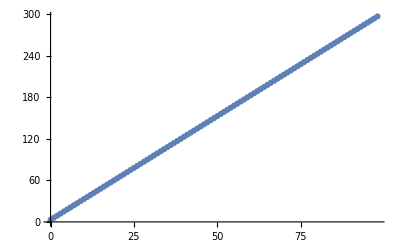

{{0,3},{1,6},{2,9},{3,12},{4,15},{5,18},{6,21},{7,24},{8,27},{9,30},{10,33},{11,36},{12,39},{13,42},{14,45},{15,48},{16,51},{17,54},{18,57},{19,60},{20,63},{21,66},{22,69},{23,72},{24,75},{25,78},{26,81},{27,84},{28,87},{29,90},{30,93},{31,96},{32,99},{33,102},{34,105},{35,108},{36,111},{37,114},{38,117},{39,120},{40,123},{41,126},{42,129},{43,132},{44,135},{45,138},{46,141},{47,144},{48,147},{49,150},{50,153},{51,156},{52,159},{53,162},{54,165},{55,168},{56,171},{57,174},{58,177},{59,180},{60,183},{61,186},{62,189},{63,192},{64,195},{65,198},{66,201},{67,204},{68,207},{69,210},{70,213},{71,216},{72,219},{73,222},{74,225},{75,228},{76,231},{77,234},{78,237},{79,240},{80,243},{81,246},{82,249},{83,252},{84,255},{85,258},{86,261},{87,264},{88,267},{89,270},{90,273},{91,276},{92,279},{93,282},{94,285},{95,288},{96,291},{97,294},{98,297}}

run6may21no4

```mathematica
stream=OpenRead["run20apr21no3"];
list=ReadList[stream];
Close[stream];
wstream=OpenWrite["run6may21no4"];
degrees={};
For[n=-1,n<98,n++;
data={};
For[k=0,k<298,k++;
m=list[[k,1]];
srs=list[[k,2]];
ns=Normal[srs/.x->(2^6*m^3*x)]; (*need srs=list[[k,2]], ns = Normal[srs], etc. *)
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,-1];
collect2=Collect[collect1/cf,x];
cf=Coefficient[collect2,x,n];
AppendTo[data,{m,cf}]
]; (* k *)
ip=InterpolatingPolynomial[data,x];
ip=Collect[ip,x];
Write[wstream,{n,ip}];
AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Print[degrees];
Close[wstream]
```

```mathematica
stream=OpenRead["run6may21no4"];
list=ReadList[stream];
Close[stream];
Print[Length[list]]
```

99

#### Clause 1

```mathematica
stream=OpenRead["run6may21no4"];
list=ReadList[stream];
Close[stream];
For[k=0,k<2,k++;
n=list[[k,1]];
poly=list[[k,2]];
degree=Exponent[poly,x];
Print["-----------------------------------------------------------------"];
Print["n: ",n," degree ",degree];
Print[factorIntoIrreducibleMonics[poly]]]
```

-----------------------------------------------------------------

n: 0 degree 3

{{24,1},{1,1},{x,1},{4/3+x^2,1}}

-----------------------------------------------------------------

n: 1 degree 6

{{276,1},{1,1},{x,2},{-16/23-(8 x^2)/69+x^4,1}}

```mathematica
streamJ=OpenRead["run6may21no4"];
listJ=ReadList[streamJ];
Close[streamJ];
streaMjnew=OpenRead["run14sept20no8"];
lisTjNew=ReadList[streaMjnew];
Close[streaMjnew];
For[k=0,k<2,k++;
Print["============================================================================="];
n=listJ[[k,1]];
srs=listJ[[k,2]];
srs=Series[srs,{x,0,5}];
Print["n: ",n];
Print[srs];
Print["--------------------------------------------------------------------------"];
n=lisTjNew[[k+1,1]];
srs=lisTjNew[[k+1,2]];
srs=Series[srs,{x,0,5}];
Print["n: ",n];
Print[srs]]
```

=============================================================================

n: 0

32 x+24 x^3+O[x]^6

--------------------------------------------------------------------------

n: 0

32 x+24 x^3+O[x]^6

=============================================================================

n: 1

-192 x^2-32 x^4+O[x]^6

--------------------------------------------------------------------------

n: 1

-192 x^2-32 x^4+O[x]^6

```mathematica
streamJ=OpenRead["run6may21no4"];
listJ=ReadList[streamJ];
Close[streamJ];
streaMjnew=OpenRead["run14sept20no8"];
lisTjNew=ReadList[streaMjnew];
Close[streaMjnew];
For[k=0,k<2,k++;
Print["============================================================================="];
n=listJ[[k,1]];
srs=listJ[[k,2]];
srs=Series[srs,{x,0,5}];
Print["n: ",n];
Print[srs];
Print["--------------------------------------------------------------------------"];
n=lisTjNew[[k,1]];
srs=lisTjNew[[k,2]];
srs=Series[srs,{x,0,5}];
Print["n: ",n];
Print[srs]]
```

=============================================================================

n: 0

32 x+24 x^3+O[x]^6

--------------------------------------------------------------------------

n: -1

1

=============================================================================

n: 1

-192 x^2-32 x^4+O[x]^6

--------------------------------------------------------------------------

n: 0

32 x+24 x^3+O[x]^6

```mathematica
streamJ=OpenRead["run6may21no4"];
listJ=ReadList[streamJ];
Close[streamJ];
streaMjnew=OpenRead["run14sept20no8"]; (* from jNew.nb *)
lisTjNew=ReadList[streaMjnew];
Close[streaMjnew];
For[k=0,k<2,k++;
Print["============================================================================="];
n=listJ[[k,1]];
srs=listJ[[k,2]];
srs=Series[srs,{x,0,5}];
Print["n: ",n];
Print[srs];
Print["--------------------------------------------------------------------------"];
n=lisTjNew[[k+1,1]];
srs=lisTjNew[[k+1,2]];
srs=Series[srs,{x,0,5}];
Print["n: ",n];
Print[srs]]
```

=============================================================================

n: 0

32 x+24 x^3+O[x]^6

--------------------------------------------------------------------------

n: 0

32 x+24 x^3+O[x]^6

=============================================================================

n: 1

-192 x^2-32 x^4+O[x]^6

--------------------------------------------------------------------------

n: 1

-192 x^2-32 x^4+O[x]^6

```mathematica
streamJ=OpenRead["run6may21no4"];
listJ=ReadList[streamJ];
Close[streamJ];
streaMjnew=OpenRead["run14sept20no8"];
lisTjNew=ReadList[streaMjnew];
Close[streaMjnew];
mn=Min[Length[listJ],Length[lisTjNew]-1];
bad=0;
For[k=0,k<mn,k++;

n=listJ[[k,1]];
srs=listJ[[k,2]];
pair1={n,srs};

n2=lisTjNew[[k+1,1]];
srs2=lisTjNew[[k+1,2]];
pair2={n,srs2};
If[pair1≠pair2,bad++]];
Print[bad]
```

0